# Plot Introduction

Lesson: 2D Plotshttps://vimeo.com/ondemand/mathematica/786832307Nonehttps://vimeo.com/ondemand/mathematica/786832307HyperlinkActionRecycledHyperlinkActive
Course: Mathematica Essentials

## Basic Plots

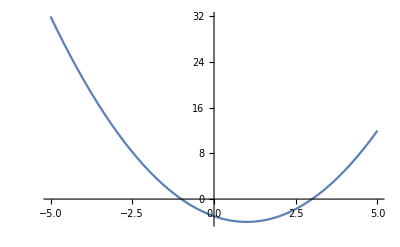

```mathematica
Plot[x^2-2x-3,{x,-5,5}]
```

## Resizing Plots

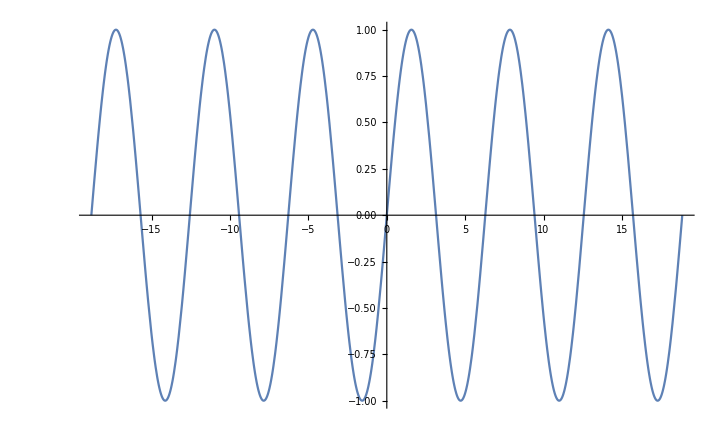

```mathematica
Plot[Sin[x],{x,-6π,6π}]
```

## Aspect Ratio

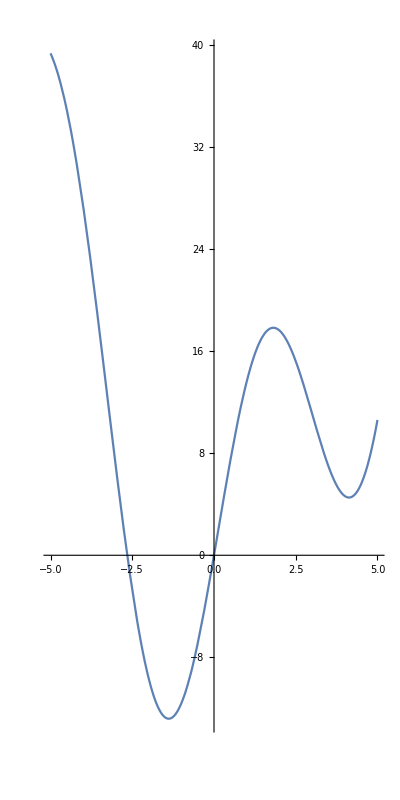

```mathematica
Plot[x^2+15Sin[x],{x,-5,5},AspectRatio->2]
```

## Multiple Plots

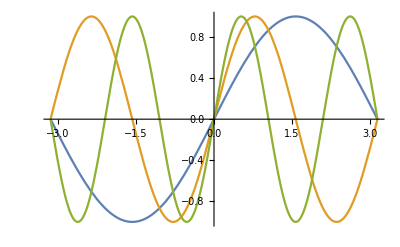

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,-π,π}]
```

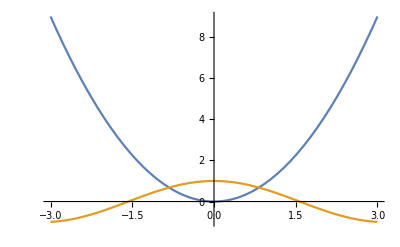

```mathematica
Plot[{x^2,Cos[x]},{x,-3,3}]
```

## Basic Styling

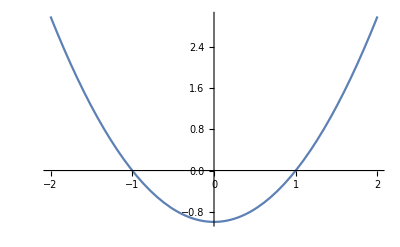

```mathematica
Plot[x^2-1,{x,-2,2},Ticks->None]
```

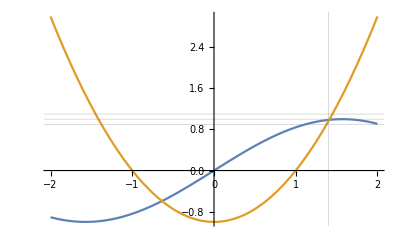

```mathematica
Plot[{Sin[x],x^2-1},{x,-2,2},GridLines->{{1.4},{0.9,1,1.1}}]
```

## PlotRange

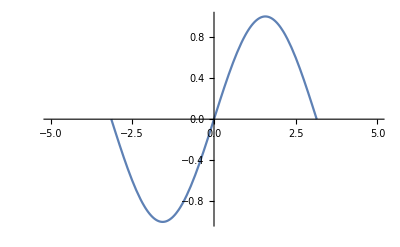

```mathematica
Plot[Sin[x],{x,-π,π},PlotRange->{{-5,5},All}]
```

## Ticks

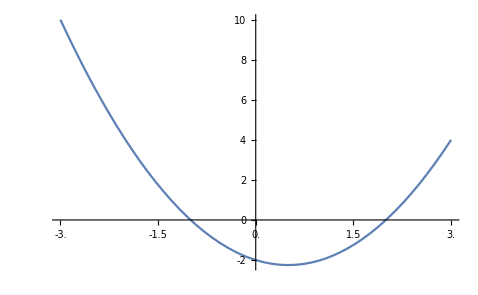

```mathematica
Plot[x^2-x-2,{x,-3,3},Ticks->{Range[-3,3,0.5],Range[-2,10]}]
```

## Multiple Options

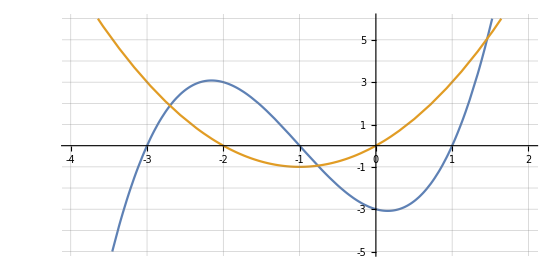

```mathematica
Plot[{x^3+3 x^2-x-3,x^2+2x},{x,-5,5},
	PlotRange->{{-4,2},{-5,6}},
	GridLines->{Range[-4,2],Range[-5,6]},
	Ticks->{Range[-4,2],Range[-5,6]},
	AspectRatio->0.5
]
```